## 3.029 Spring 2022 Lecture 12 - 03/09/2022

## Step-Growth Polymerization

Last lecture, we developed a reptation model for a single polymer chain

Today, we will investigate the collision-free reptation of multiple chains

And use it to investigate step-growth polymerization

## Initialization Functions from L10

Making a 2D correlated polymer

```mathematica
angularRange[correlation_]:={-1,1}(1-correlation)2π/3

collisionQ[nf_NearestFunction,bondLength_:1][candidatePt_]:=First[nf[candidatePt]]["Distance"]<bondLength

addCorrelatedParticleToChain[correlation_][chainSoFar_]:=Block[{

nf=Nearest[chainSoFar->All],
angleRange=angularRange[correlation],
lastAngle=ArcTan@@(chainSoFar[[-1]]-chainSoFar[[-2]]),
newAngle,candidate,collision

},

newAngle=RandomReal[angleRange]+lastAngle;
candidate=Last[chainSoFar]+AngleVector[newAngle];

collision=collisionQ[nf][candidate];
If[collision,chainSoFar,Append[chainSoFar,candidate]]

]/;Length[chainSoFar]>1

correlatedPolymerChain2D[numberUnits_,correlation_]:=AnglePath[RandomReal[angularRange[correlation],numberUnits-1]]

Clear[collisionFreeCorrelatedPolymerChain2D]
collisionFreeCorrelatedPolymerChain2D[numberUnits_,correlation_,origin_:{0,0},maxAttempts_:100]:=With[{start=Join[{origin},{AngleVector[origin,RandomReal[angularRange[correlation]]]}]},
NestWhile[addCorrelatedParticleToChain[correlation],start,Length[#]<numberUnits&,1,maxAttempts]
]

chainGraphic[positions_]:= {
{Circle[#,1/2]&/@positions[[2;;-2]]},
{FaceForm[LightGray],EdgeForm[Black],Disk[#,1/2]&/@positions[[{1,-1}]]}
}
```

Single chain reptation

```mathematica
collisionFreeQ[positions_]:=With[{nf=Nearest[positions]},Total[Length[nf[#,{All,1.-10^-6}]]&/@positions]<=Length[positions]]

moveSingleChain[ positions_,ds_,stickiness_:0.1]:= 
Block[{newPositions},
newPositions= displacements[RandomInteger[{1,Length[positions]}],positions,ds,stickiness,RandomReal[2π]];
If[collisionFreeQ[newPositions],newPositions,positions]
]

displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },

Δ=precompute[positionList,perturbedIndex,s,ν,θ];

newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];

newPositions[index_] := newPositions[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex]},
newPositions[nextIndex] + Δ[[index]]
];

newPositions/@Range[Length[Δ]]
]

precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]
```

## Multiple Chains Reptating

We wish to extend our single-chain reptation to multiple chains

But we similarly have to be concerned about collisions

We will use a hierarchical collision-detection!

We’ll use the following polymer chain to develop our collision detection

Note the functions to make this are from L10 (see collapsed section above)

```mathematica
SeedRandom[1111];
chainPositions=collisionFreeCorrelatedPolymerChain2D[12,0.4];
```

First, we start by checking if the axis-aligned bounding boxes of two chains overlap

```mathematica
axesAlignedBoundingBoxes[positions_]:={{-1/2,1/2},{-1/2,1/2}}+MinMax/@Transpose[positions]

pairWiseAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(xMaxA>xMinB&&xMinA<xMaxB)&&(yMaxA>yMinB&&yMinA<yMaxB)
```

Let’s define a new visualization function to help us with debugging bounding boxes collisions

```mathematica
chainGraphic[positions_,bb_,col_:RandomColor[]]:= {
{Opacity[0.25],col,Rectangle@@Transpose[bb]},
{FaceForm[None],EdgeForm[col//Darker],Disk[#,1/2]&/@positions[[2;;-2]]},
{FaceForm[col//Darker],EdgeForm[Black],Disk[#,1/2]&/@positions[[{1,-1}]]}
}
```

We construct the bounding box for our polymer chain

and check whether it intersects with the bounding box of another chain

for simplicity, we use the same chain - just translated

True

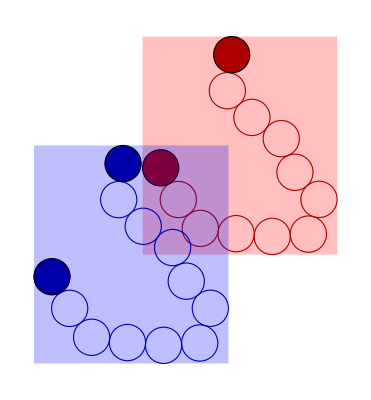

```mathematica
Block[{posA=chainPositions,posB=TranslationTransform[{-3,-3}]@chainPositions,bbA,bbB},

bbA=axesAlignedBoundingBoxes[posA];
bbB=axesAlignedBoundingBoxes[posB];

pairWiseAxesAlignedIntersection[bbA,bbB]//Echo;

Graphics[MapThread[chainGraphic,{{posA,posB},{bbA,bbB},{Red,Blue}}]]

]
```

Great, our bounding-box collision detection seems to work!

Next, we only keep points on each chain inside the overlap region

```mathematica
returnPointsInOverlapSimple[{positionsA_,{{xMinA_,xMaxA_},{yMinA_,yMaxA_}}},{positionsB_,{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}}]:=With[
{
xMin=Max[xMinA,xMinB]-1/2,yMin=Max[yMinA,yMinB]-1/2,
xMax=Min[xMaxA,xMaxB]+1/2,yMax=Min[yMaxA,yMaxB]+1/2
},
Table[Select[pos,xMax>#[[1]]>xMin&&yMax>#[[2]]>yMin&],{pos,{positionsA,positionsB}}]
]
```

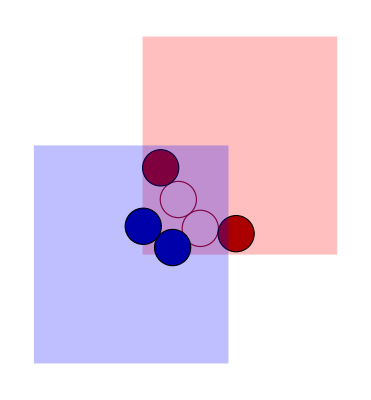

```mathematica
Block[{posA=chainPositions,posB=TranslationTransform[{-3,-3}]@chainPositions,bbA,bbB},

bbA=axesAlignedBoundingBoxes[posA];
bbB=axesAlignedBoundingBoxes[posB];

{posA,posB}=returnPointsInOverlapSimple[{posA,bbA},{posB,bbB}];

Graphics[MapThread[chainGraphic,{{posA,posB},{bbA,bbB},{Red,Blue}}]]

]
```

This again seems to work well, and reduces the problem considerably

Quick note: Later, we will concern ourselves with the exact position of collisions

To check e.g. if an end-mer collided with another end-mer

As such, we’ll need to update this function later to also return the indices of the selected points

If the two chains are non-empty, we finally check pairwise distances

```mathematica
Block[{posA=chainPositions,posB=TranslationTransform[{-3,-3}]@chainPositions,bbA,bbB,dm},

bbA=axesAlignedBoundingBoxes[posA];
bbB=axesAlignedBoundingBoxes[posB];

{posA,posB}=returnPointsInOverlapSimple[{posA,bbA},{posB,bbB}];

MatrixForm[
dm=DistanceMatrix[posA,posB]
]//Echo;

Min[dm]<1

]
```

(2.22098 | 1.68108
1.33284 | 1.21777
0.928771 | 1.57581
1.79453 | 2.57211)

True

Remember our discussion on checking pairwise distances last lecture

We can do a little faster by looping over a Nearest function until we find the first distance less than 1

```mathematica
shortestDistanceLessThanOne[posA_,posB_]:=Block[{nf=Nearest[posA->"Distance"],i=1,d=2.,l=Length[posB]},
While[d>1. && i<=l,
d=First[nf[posB[[i]]]];
i++
];
d<1.
]
```

```mathematica
Block[{posA=chainPositions,posB=TranslationTransform[{-3,-3}]@chainPositions,bbA,bbB,dm},

bbA=axesAlignedBoundingBoxes[posA];
bbB=axesAlignedBoundingBoxes[posB];

{posA,posB}=returnPointsInOverlapSimple[{posA,bbA},{posB,bbB}];

shortestDistanceLessThanOne[posA,posB]

]
```

True

The final piece we need is a connectivity matrix telling us which bounding boxes overlap

We’ll construct this by looking at the upper-triangle part of the matrix at each step

```mathematica
Subsets[Range[6],{2}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}

```mathematica
MatrixForm[SparseArray[Subsets[Range[6],{2}]->1]]
```

(0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1)

Is this efficient? How can we do better?

```mathematica
Clear[connectivityMatrixIndex,connectivityMatrix]

connectivityMatrixIndex[bbs_,{i_,j_}]:=pairWiseAxesAlignedIntersection[bbs[[i]],bbs[[j]]]//Boole

connectivityMatrix[bbs_]:=Block[{s=Subsets[Range[Length[bbs]],{2}],l=Length[bbs],is},
SparseArray[s->(connectivityMatrixIndex[bbs,#]&/@s),{l,l}]
]
```

Connectivity Matrix  (0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

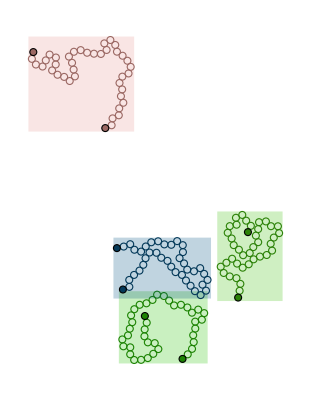

```mathematica
(*SeedRandom[1111];*)
SeedRandom[11111];
listOfPositions=Table[collisionFreeCorrelatedPolymerChain2D[40,0.3,RandomReal[{-30,30},2]],4];
bbs=axesAlignedBoundingBoxes/@listOfPositions;
cols=RandomColor[4];
Echo[MatrixForm[connectivityMatrix[bbs]],"Connectivity Matrix"];
graphicMultiple=Graphics[MapThread[chainGraphic,{listOfPositions,bbs,cols}]]
```

Wrapping it all together

```mathematica
pairwiseChainCollisionQ[{listOfPositions_,bbs_},{i_,j_}]:=Block[{
posA=listOfPositions[[i]],bbA=bbs[[i]],
posB=listOfPositions[[j]],bbB=bbs[[j]]
},

{posA,posB}=returnPointsInOverlapSimple[{posA,bbA},{posB,bbB}];
If[Length[posA]==0||Length[posB]==0,False,shortestDistanceLessThanOne[posA,posB]]
]

collisionsFreeChainsQ[listOfPositions_]:=Block[{
bbs=axesAlignedBoundingBoxes/@listOfPositions,
mij,nonzero},

mij=connectivityMatrix[bbs];
nonzero=mij["NonzeroPositions"];


NoneTrue[nonzero,pairwiseChainCollisionQ[{listOfPositions,bbs},#]&]

]

moveAllChains[listOfPositions_,ds_]:= Block[{listOfPos=listOfPositions},
listOfPos=moveSingleChain[#,ds]&/@listOfPos;
If[collisionsFreeChainsQ[listOfPos],listOfPos,listOfPositions]
]
```

```mathematica
Dynamic[Graphics[MapThread[chainGraphic,{listOfPositions,bbs,cols}]]]
```

```mathematica
Do[
listOfPositions=moveAllChains[listOfPositions,.1];
bbs=axesAlignedBoundingBoxes/@listOfPositions;
Pause[0.01],
{1000}]
```

$Aborted

## Step-Growth Polymerization

Now that we have a realistic motion for polymer chains in 2D

We’ll try and simulate one of the important polymerization mechanisms, called step-growth

Our approach is again simple:

We will start with many non-colliding polymer dimers and allow them to reptate

When we detect a collision between two ‘end-mers’ we will merge our chains (to form 4-mers, 6-mers, 8-mers etc)

First, let’s start with our initial dimers configuration

We could do this a number of ways

E.g. we could start with a regular hexagonal arrangement of dimers

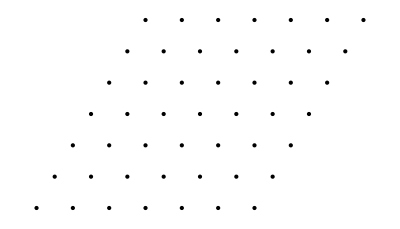

```mathematica
hexagonalLatticeVectors={{1,0},{1/2,Sqrt[3]/2}};latticeCoords=Tuples[Range[-12,12,4],2];
hexagonalLatticePoints=latticeCoords.hexagonalLatticeVectors;
Graphics[{Point[hexagonalLatticePoints]}]
```

And place a dimer on each hexagonal grid point within a square box

```mathematica
randomDimer[origin_]:=Join[{origin},{AngleVector[origin,RandomReal[2π]]}]
```

```mathematica
hexagonalDimerConfiguration[size_]:=Block[{
hexagonalLatticeVectors={{1,0},{1/2,Sqrt[3]/2}},latticeCoords=Tuples[Range[-size,size,4],2],
pts,dimers,bbs,collisions},

pts=Select[latticeCoords.hexagonalLatticeVectors,size/2>#[[1]]>-size/2&&size/2>#[[2]]>-size/2&];

randomDimer/@pts

]
```

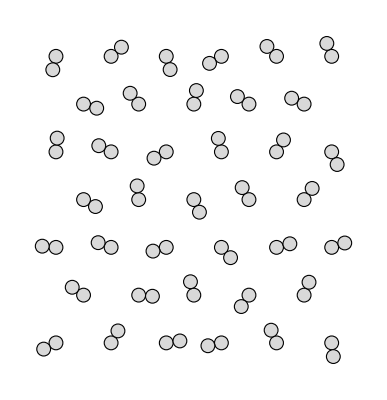

```mathematica
Graphics[chainGraphic/@hexagonalDimerConfiguration[24]]
```

Or equivalently, we can make an amorphous packing of lattice sites for each of our dimers

```mathematica
amorphousPackedDimers[size_]:=Block[{
proc=HardcorePointProcess[1,4,2],sites},
sites=RandomPointConfiguration[proc,Rectangle[{-size/2,-size/2},{size/2,size/2}]]["Points"];
randomDimer/@sites

]
```

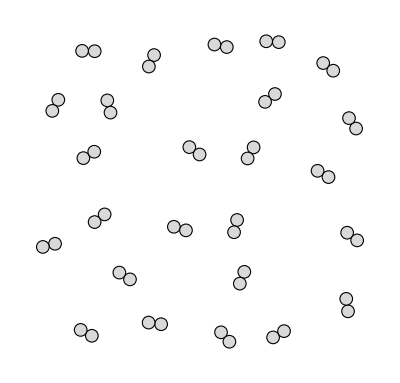

```mathematica
Graphics[chainGraphic/@amorphousPackedDimers[24]]
```

First, like we mentioned above, we generalize our overlapping bounding boxes function to return the indices of the points as-well

```mathematica
returnPointsInOverlap[{positionsA_,{{xMinA_,xMaxA_},{yMinA_,yMaxA_}}},{positionsB_,{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}}]:=With[
{
xMin=Max[xMinA,xMinB]-1/2,yMin=Max[yMinA,yMinB]-1/2,
xMax=Min[xMaxA,xMaxB]+1/2,yMax=Min[yMaxA,yMaxB]+1/2
},
Table[Select[Thread[{pos,Range[Length[pos]]}],xMax>#[[1,1]]>xMin&&yMax>#[[1,2]]>yMin&],{pos,{positionsA,positionsB}}]
]
```

```mathematica
Block[{posA=chainPositions,posB=TranslationTransform[{-3,-3}]@chainPositions,bbA,bbB,dm},

bbA=axesAlignedBoundingBoxes[posA];
bbB=axesAlignedBoundingBoxes[posB];

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];

Echo[posA];
Echo[posB];

Graphics[MapThread[chainGraphic,{{posA[[All,1]],posB[[All,1]]},{bbA,bbB},{Red,Blue}}]]

]
```

{{{0,0},1},{{0.4879,-0.8729},2},{{1.09396,-1.66832},3},{{2.08326,-1.81421},4}}

{{{0.329881,-2.19634},9},{{-0.480803,-1.61086},10}}

-Graphics-

This allows us to check for  collisions, while maintaining the relative indices

remember the first and last indices are our end-mers

and thus we want to check the collision index

```mathematica
returnAllCollisions[posA_,posB_]:=Block[{nf,sorted,
posShortcoords,posShortIndices,
posLongcoords,posLongIndices,
cols},

sorted=SortBy[{posA,posB},Length];
posShortcoords=sorted[[1,All,1]];posShortIndices=sorted[[1,All,2]];
posLongcoords=sorted[[2,All,1]];posLongIndices=sorted[[2,All,2]];

nf=Nearest[posLongcoords->{"Index","Distance"}];

cols=Select[Prepend[First[nf[posShortcoords[[#]]]],#]&/@Range[Length[posShortcoords]],#[[3]]<1&];

{posLongIndices[[#2]],posShortIndices[[#1]],#3}&@@@cols

]
```

In this case, we detect a single collision

Between the 3rd and 9th particle

These are both inside the middle of the chain, so no further action needs to be taken

```mathematica
Block[{posA=chainPositions,posB=TranslationTransform[{-3,-3}]@chainPositions,bbA,bbB,dm},

bbA=axesAlignedBoundingBoxes[posA];
bbB=axesAlignedBoundingBoxes[posB];

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];

returnAllCollisions[posA,posB]//Echo;

Graphics[MapThread[chainGraphic,{{posA[[All,1]],posB[[All,1]]},{bbA,bbB},{Red,Blue}}]]
]
```

{{3,9,0.928771}}

-Graphics-

```mathematica
pairwiseChainCollisions[{listOfPositions_,bbs_},{i_,j_}]:=Block[{
posA=listOfPositions[[i]],bbA=bbs[[i]],
posB=listOfPositions[[j]],bbB=bbs[[j]]
},

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];
If[Length[posA]==0||Length[posB]==0,{},returnAllCollisions[posA,posB]]
]
```

When the collision is between some of the end-mers however,

we wish to join the the two chains

this will depend on the ordering of the colliding end-mers

I.e. is it a head-head collision? a head-tail collision etc?

```mathematica
compareEndPoints[listOfPositions_,{i_,j_}]:=
Block[{
endsI=listOfPositions[[i,{1,-1}]],
endsJ=listOfPositions[[j,{1,-1}]],
vecs},

vecs=Tuples[{endsI,endsJ}];
Thread[SquaredEuclideanDistance@@@vecs<1]
]
```

```mathematica
mergeEndPoints[listOfPositions_,{i_,j_},pairwiseEndPointChecks_]:=With[{posI=listOfPositions[[i]],posJ=listOfPositions[[j]]},
Switch[pairwiseEndPointChecks,
{True,_,_,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{Reverse[posI],posJ}]],
{False,True,_,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posJ,posI}]],
{False,False,True,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posI,posJ}]],
{False,False,False,True},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posI,Reverse[posJ]}]],
_,listOfPositions
]
]
```

```mathematica
checkProposedMerger[{i_,j_},{posI_,posJ_}]:=
With[{proposal=Join[posI,posJ]},
If[collisionFreeFurtherQ[proposal],{{i},{j}}->proposal,Echo["Intersecting Merger"];{}]
]
```

```mathematica
collisionFreeFurtherQ[positions_]:=With[{nf=Nearest[positions->All],l=Length[positions]},
Length[Join@@Table[Select[nf[positions[[i]],{All,1}],Abs[#Index-i]>1&],{i,l}]]==0]
```

Let’s wrap everything together

```mathematica
checkForCollisions[{listOfPositions_,oldListOfPositions_}]:=Catch[
Block[{
listOfPos=listOfPositions,
bbs=axesAlignedBoundingBoxes/@listOfPositions,
mij,nonzero,collisions,collisionIndices,endpointChecks,lengths},

mij=connectivityMatrix[bbs];
If[mij["ExplicitLength"]==0,Echo["No Bounding Box Collisions"];Return[listOfPos]];

nonzero=mij["NonzeroPositions"];
collisions=pairwiseChainCollisions[{listOfPos,bbs},#]&/@nonzero;
If[Length[Join@@collisions]==0,Echo["No Collisions"];Return[listOfPos]];

lengths=Sort[Length/@Extract[listOfPos,List/@#]]&/@nonzero;

Do[
If[
Length[collisions[[a]]]>0&&
(1<collisions[[a,j,1]]<lengths[[a,1]]||
1<collisions[[a,j,2]]<lengths[[a,2]]),
Echo["No-terminating collisions"];Throw[oldListOfPositions]],{a,Length[collisions]},{j,Length[collisions[[a]]]}];

collisionIndices= Extract[nonzero,Position[collisions,Except[{}],1,Heads->False]];
endpointChecks=compareEndPoints[listOfPos,#]&/@collisionIndices;
If[Nor@@Flatten[endpointChecks],Echo["No Mergers"];Return[oldListOfPositions]];

Do[
listOfPos=mergeEndPoints[listOfPos,collisionIndices[[a]],endpointChecks[[a]]],
{a,Length[collisionIndices]}
];

DeleteDuplicates[listOfPos]

]
]
```

```mathematica
moveAllChains[listOfPositions_,ds_]:= Block[{listOfPos=listOfPositions},
listOfPos=moveSingleChain[#,ds]&/@listOfPos;
checkForCollisions[{listOfPos,listOfPositions}]
]
```

```mathematica
listOfPositions=amorphousPackedDimers[35];
Dynamic[Graphics[chainGraphic/@listOfPositions]]
```

```mathematica
QuietEcho[
Do[
listOfPositions=moveAllChains[listOfPositions,.1],
{5000}]
]
```

$Aborted